## (x^2-1)^2

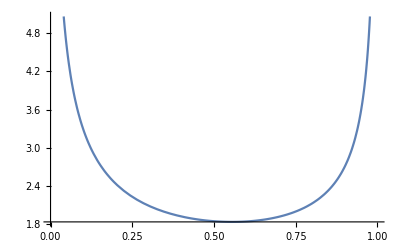

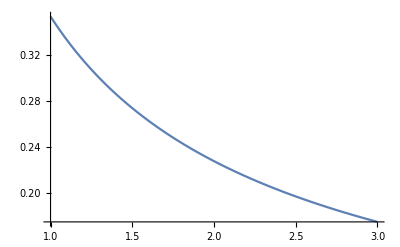

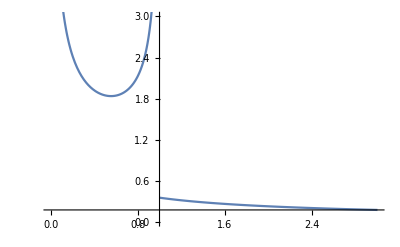

```mathematica
Plot[(1/(2 √t))(1/√(1+√t)+1/√(1-√t)) , {t,0,1}]
Plot[(1/(2 √t))(1/√(1+√t)) , {t,1,3}]
Show[%,%%,PlotRange->{{0,3},{0,3}}]
```

```mathematica
NIntegrate[(1/(2 √t))(1/√(1+√t)+1/√(1-√t)) ⅇ^-t, {t,0,1}]
NIntegrate[(1/(2 √t))(1/√(1+√t)) ⅇ^-t, {t,1,10}]
%+%%
```

1.88175

0.0919799

1.97373

```mathematica
NIntegrate[ⅇ^(-(x^2-1)^2), {x,-∞,∞}]
```

1.97373

```mathematica
NIntegrate[ⅇ^(-(x^2-1)^2), {x,-√2,√2}]
```

1.88175

```mathematica
(1/(2 √t))(1/√(1+√t)+1/√(1-√t))
Series[√t%,{t,0,1}]
Series[√(1-t)%%, {t,1,1}]
N[(1/(2 √t))(1/√(1+√t))/.t->1]
```

(1/(√(1-√t))+1/(√(1+√t)))/(2 √t)

1+(3 t)/8+O[t]^(3/2)

1/(√2)+(√(1-t) √(t-1))/(2 √2 √(-1+t))-(3 (t-1))/(8 √2)+O[t-1]^(3/2)

0.353553

## Quartic

```mathematica
Sum[(-x)^k / (k!)^2, {k,0,∞}]
Sum[(x)^k / (k!)^2, {k,0,∞}]
```

BesselJ[0,2 √x]

BesselI[0,2 √x]

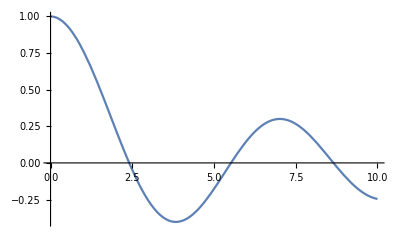

```mathematica
Plot[BesselJ[0,x], {x,0,10}]
```

```mathematica
action = x^2/2 + z x^4/4
Integrate[ⅇ^-action, {x,-∞,∞}]
```

x^2/2+(x^4 z)/4

ConditionalExpression[(ⅇ^(1/8/z) BesselK[1/4,1/(8 z)])/(√2 √z), Re[z]>0]

```mathematica
Integrate[ⅇ^(-x^2/2)BesselJ[0,2 √(z t x^4/4)], {x,-∞,∞}]
```

ConditionalExpression[(2 √(2/π) EllipticK[1/2-1/(2 √(1+4 t z))])/(1+4 t z)^(1/4), Im[√(t z)]>0||Re[√(t z)]>0]

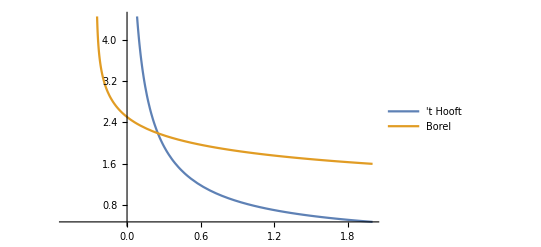

```mathematica
Plot[{2 √(z/(√(4t z + 1)-1))1/(√(4t z + 1)) /. z->1, (2 √(2/π) EllipticK[1/2-1/(2 √(1+4 t z))])/(1+4 t z)^(1/4)/.z->1},{t,-1/2,2}, PlotLegends->{"'t Hooft", "Borel"}]
```

```mathematica
zval=100;
N[(ⅇ^(1/8/z) BesselK[1/4,1/(8 z)])/(√2 √z) /. z->zval]
NIntegrate[2 √(z/(√(4t z + 1)-1))1/(√(4t z + 1)) ⅇ^-t /. z->zval, {t,0,∞}]
NIntegrate[(2 √(2/π) EllipticK[1/2-1/(2 √(1+4 t z))])/(1+4 t z)^(1/4) ⅇ^-t /. z->zval, {t,0,∞}]
```

0.78429

0.78429

0.78429

```mathematica
Integrate[ⅇ^(-x^2/2) (x^4/4)^k, {x,-∞,∞}]
```

ConditionalExpression[√2 Gamma[1/2+2 k], Re[k]>-1/4]

```mathematica
Sum[√2 Gamma[1/2+2 k] (-t)^k / (k!)^2, {k,0,∞}]
```

(2 √(2/π) EllipticK[(-1+√(1+4 t))/(2 √(1+4 t))])/(1+4 t)^(1/4)

```mathematica
Series[EllipticK[x], {x,0,1}]
```

π/2+(π x)/8+O[x]^2

## Inverse Laplace

```mathematica
LaplaceTransform[1, t, s]
```

1/s

```mathematica
LaplaceTransform[ⅇ^t, t, s]
```

1/(-1+s)

```mathematica
LaplaceTransform[1/(√t), t, s]
```

(√π)/(√s)

```mathematica
InverseLaplaceTransform[1/(√s), s, t]
```

1/(√π √t)

```mathematica
InverseLaplaceTransform[s^α, s, t]
```

t^(-1-α)/Gamma[-α]

```mathematica
invlapF[t_] := 2 √(1/(-1+√(4t+1)))1/(√(4t+1))
invlapG[t_] := 1/(√(π t))
invlapB[t_] := (2 √(2/π) EllipticK[1/2-1/(2 √(1+4 t))])/(1+4 t)^(1/4)
```

```mathematica
tval=1;
NIntegrate[invlapF[x] invlapG[tval-x], {x,0,tval}]
N[invlapB[tval]]
```

1.81452

1.81452

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.250943}. NIntegrate obtained -1.43882-1.54763 ⅈ and 0.0172518 for the integral and error estimates.

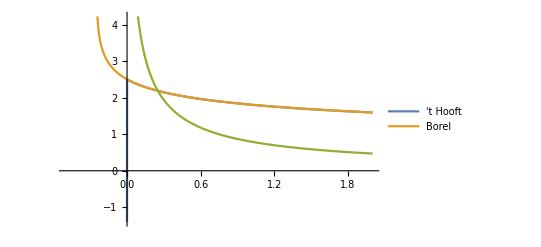

```mathematica
Plot[{NIntegrate[invlapF[x] invlapG[t-x], {x,0,t}], invlapB[t],invlapF[t]},{t,-1/2,2}, PlotLegends->{"'t Hooft", "Borel"}]
```

```mathematica
Integrate[1/√((s-a) (t-s)), {s,a,t}, Assumptions->t>a]
```

π

```mathematica
Integrate[1/√((s-a) (t-s)), {s,a,t}]
```

-2 √(1/(a-t)) √(-a+t) ArcSinh[(√(a-t))/(√(-a+t))]

-2 √(1/(1-t)) √(-1+t) ArcSinh[(√(1-t))/(√(-1+t))]

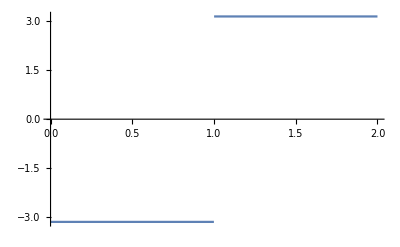

```mathematica
FullSimplify[%625, Assumptions->a==1&&t>0]
Plot[%, {t,0,2}]
```

```mathematica
Integrate[1/√((a-s)(t-s)), {s,0,t}, Assumptions->t<a]
```

```mathematica
ConditionalExpression[2 ArcCosh[√(a/(a-t))], t>0]
```

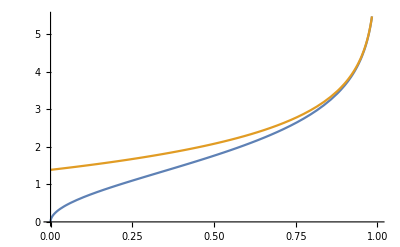

```mathematica
Plot[{2 ArcCosh[√(1/(1-t))], Log[4/(1-t)]}, {t,0,1}]
```

```mathematica
FullSimplify[Series[2 ArcCosh[√(a/ϵ)], {ϵ,0,1}], Assumptions->ϵ>0&&a>0]
```

Log[(4 a)/ϵ]-ϵ/(2 a)+O[ϵ]^2

```mathematica
Integrate[2 ArcCosh[√(a/(a-t))] ⅇ^-a, {t,0,a}, Assumptions->a>0]
```

2 a ⅇ^-a

```mathematica
f0[t_]:=1/(2 √t)(1/(√(1+√t))+1/(√(1-√t)))
f1[t_]:=1/(2 √t)1/(√(1+√t))
g[t_]:=1/(√(π t))
```

```mathematica
tval=1-0.000000000001;
NIntegrate[f0[s]g[tval-s], {s,0,tval}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.99999998318286630028326742749491694208646697106246392650064080954}. NIntegrate obtained 12.7599 and 0.817966 for the integral and error estimates.

12.7599

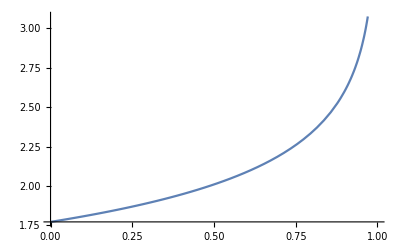

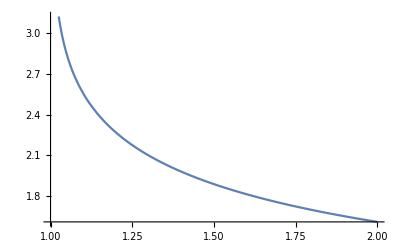

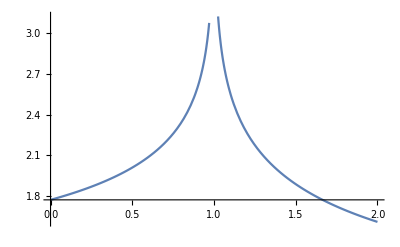

```mathematica
Plot[NIntegrate[f0[s]g[t-s], {s,0,t}], {t,0,1}]
Plot[NIntegrate[f0[s]g[t-s], {s,0,1}] + NIntegrate[f1[s]g[t-s], {s,1,t}], {t,1,2}]
Show[%%,%,PlotRange->Full]
```

```mathematica
NIntegrate[f0[s]g[t-s] ⅇ^-t, {t,0,1}, {s,0,t}]
NIntegrate[f0[s]g[t-s] ⅇ^-t, {t,1,∞}, {s,0,1}] + NIntegrate[f1[s]g[t-s] ⅇ^-t, {t,1,∞}, {s,1,t}]
%%+%
```

NIntegrate::zeroregion: Integration region {{0,1},{1.,0.99999999999999999999999999999997515343915057095724101573241897475}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

1.29141

0.68232

1.97373

## (x^2-a^2)^2

x^2/2-(x^3 z)/2+(x^4 z^2)/8

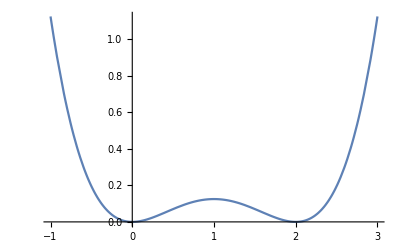

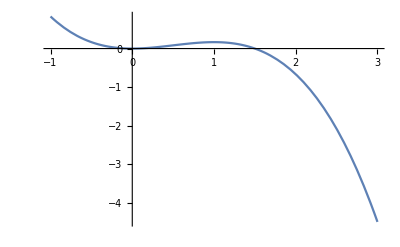

```mathematica
Expand[1/(8 a^2)(x^2-a^2)^2 /. x->x-a]/.a->1/z
Plot[%/.z->1, {x,-1,3}]
Plot[x^2/2-x^3/3, {x,-1,3}]
```

```mathematica
Integrate[ⅇ^(-x^2/2)BesselI[0,2 √(t x^3/3)], {x,-∞,∞}]
```

∫_(-∞)^∞ ⅇ^(-x^2/2) BesselI[0,(2 √(t x^3))/(√3)]ⅆx

```mathematica
NIntegrate[ⅇ^(-x^2/2)BesselI[0,2 √(t x^3/3)] /. t->0, {x,-∞,∞}]
```

2.50663

```mathematica
Integrate[ⅇ^(-x^2/2) (x^3/3)^k, {x,-∞,∞}]
```

ConditionalExpression[2^(-1/2+(3 k)/2) 3^-k (1+(-1)^k) Gamma[1/2+(3 k)/2], Re[k]>-1/3]

```mathematica
Sum[Gamma[1/2+3m] x^m / ((2m)!)^2, {m,0,∞}]
```

√π HypergeometricPFQ[{1/6,5/6},{1/2,1},(27 x)/16]

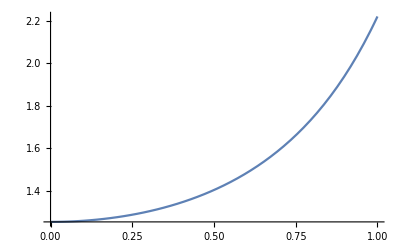

```mathematica
Plot[{(*∫_(-∞)^∞ ⅇ^(-x^2/2) BesselI[0,(2 √(t x^3))/(√3)]ⅆx,*)√(π/2) HypergeometricPFQ[{1/6,5/6},{1/2,1},(3 t^2)/2]}, {t,0,1}]
```

z^2/2-(g z^3)/3+(g^2 z^4)/18

z^2/2-1/6 ⅇ^(-ⅈ/4) z^3+1/72 ⅇ^(-ⅈ/2) z^4

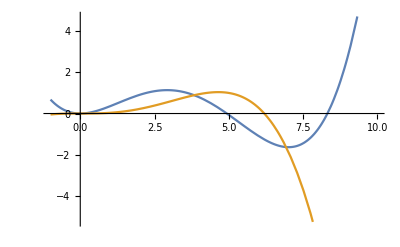

ⅇ^(-z^2/2+1/6 ⅇ^(-ⅈ/4) z^3-1/72 ⅇ^(-ⅈ/2) z^4)

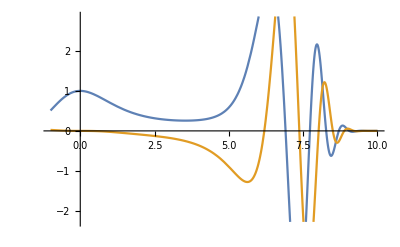

```mathematica
z^2/2 - g z^3/3 + g^2 z^4/18
%/. g->1/2 ⅇ^(-ⅈ 1/4)
Plot[{Re[%], Im[%]}, {z,-1,10}]
ⅇ^(- %%)
Plot[{Re[%], Im[%]}, {z,-1,10}]
```

(-1+(0.980067+0.198669 ⅈ) r^2)^2

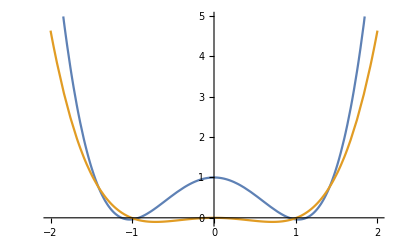

```mathematica
(z^2-1)^2 /. {z->r ⅇ^(ⅈ 0.1)}
Plot[{Re[%],Im[%]}, {r,-2,2}]
```

## x^2-x^3+x^4

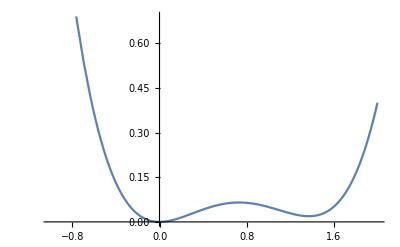

```mathematica
gval=1;
γval=1.05;
Plot[x^2/2 - 2 γval gval x^3/3 + gval^2 x^4/4, {x,-1,2}]
```

```mathematica
action = x^2/2 - 2γ x^3/3 + x^4/4
```

x^2/2+x^4/4-(2 x^3 γ)/3

```mathematica
Solve[D[action, x]==0,x]
Expand[action /. %[[2]]]
Expand[action /. %%[[3]]]
```

{{x→0},{x→γ-√(-1+γ^2)},{x→γ+√(-1+γ^2)}}

-1/4+γ^2-(2 γ^4)/3-2/3 γ √(-1+γ^2)+2/3 γ^3 √(-1+γ^2)

-1/4+γ^2-(2 γ^4)/3+2/3 γ √(-1+γ^2)-2/3 γ^3 √(-1+γ^2)

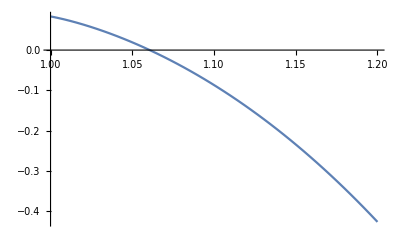

```mathematica
Plot[-1/4+γ^2-(2 γ^4)/3+2/3 γ √(-1+γ^2)-2/3 γ^3 √(-1+γ^2), {γ, 1,1.2}]
```

```mathematica
γval=21/20;
action/.γ->γval
Solve[%==t, x];
sollist=Simplify[%, Assumptions->t>0];
Length[sollist]
```

x^2/2-(7 x^3)/10+x^4/4

4

```mathematica
cm=-1/4+γ^2-(2 γ^4)/3-2/3 γ √(-1+γ^2)+2/3 γ^3 √(-1+γ^2) /.γ->γval
cp=-1/4+γ^2-(2 γ^4)/3+2/3 γ √(-1+γ^2)-2/3 γ^3 √(-1+γ^2) /.γ->γval
N[cm]
N[cp]
```

3373/80000+(287 √41)/80000

3373/80000-(287 √41)/80000

0.0651337

0.0191913

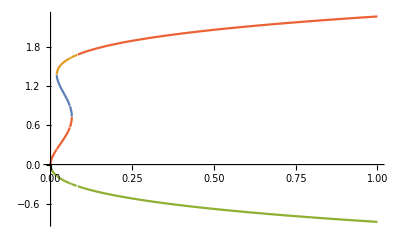

```mathematica
x/.sollist;
Plot[%, {t,0,1}, GridLines->{{cp, cm},{}}]
```

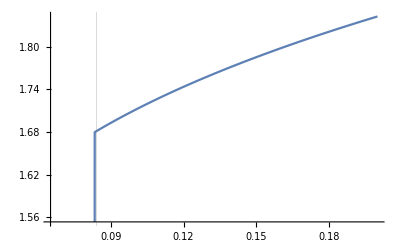

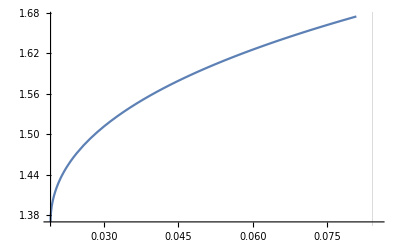

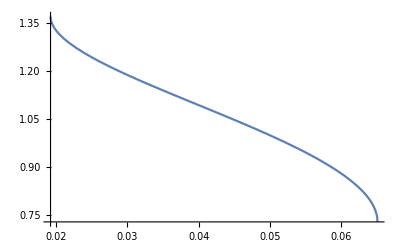

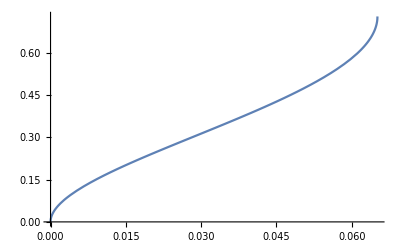

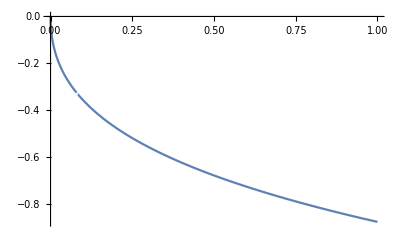

```mathematica
Plot[x/.sollist[[4]], {t,cm,0.2}, GridLines->{{cm+0.019},{}}]
Plot[x/.sollist[[2]], {t,cp,cm+0.02},GridLines->{{cm+0.019},{}}]
Plot[x/.sollist[[1]], {t,cp,cm}]
Plot[x/.sollist[[4]], {t,0,cm}]
Plot[x/.sollist[[3]], {t,0,1}]
```

```mathematica
daction=1/D[action,x] /.γ->γval
```

1/(x-(21 x^2)/10+x^3)

```mathematica
(* 0 < t < cp *)
f0 = Abs[daction/.sollist[[4]]] + Abs[daction/.sollist[[3]]];
(* cp < t < cm *)
f1 = Abs[daction/.sollist[[2]]] + Abs[daction/.sollist[[1]]] + f0;
(* cm < t < cm+0.02? *)
f2m = Abs[daction/.sollist[[2]]] + Abs[daction/.sollist[[3]]];
(* cm < t *)
f2 = f0;
```

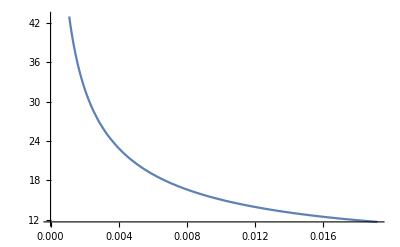

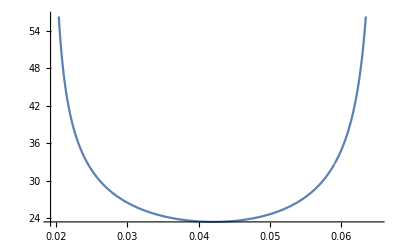

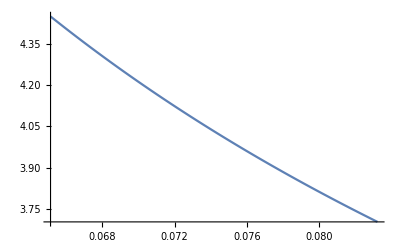

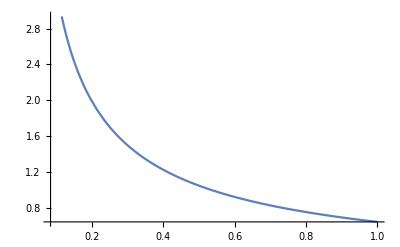

```mathematica
Plot[f0, {t,0,cp}]
Plot[f1, {t,cp,cm}, GridLines->{{cp,cm}, {}}]
Plot[f2m, {t,cm,cm+0.0181}]
Plot[f2, {t,cm+0.0181,1}]
```

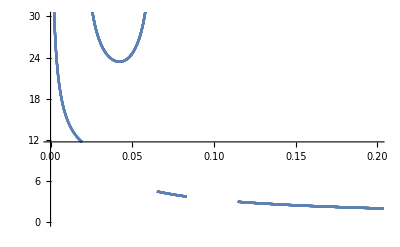

```mathematica
Show[%%%%,%%%,%%,%, PlotRange->{{0,0.2},{0,30}}, GridLines->{{cp,cm}, {}}]
```

```mathematica
ϵval=0.0001;
{Limit[f0, t->0+ϵval],Limit[f0, t->cp-ϵval]}
{Limit[f1, t->cp+ϵval],Limit[f1, t->cm-ϵval]}
{Limit[f2m, t->cm+ϵval],Limit[f2, t->∞]}
```

{141.504,11.7043}

{162.77,211.475}

{4.44673,0}

```mathematica
Limit[f2m, t->cm+0.0181]
Limit[f2, t->cm+0.0183]
```

3.70128

3.69473

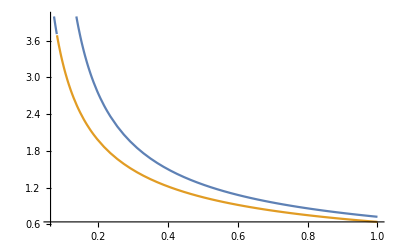
```mathematica
Show[-Graphics-, PlotRange->{{cm,cm+0.02},{3,4}},GridLines->{{cm+0.0181,cm+0.0183}, {}}]
```

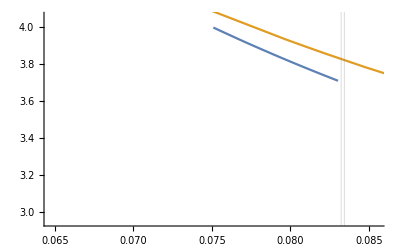

```mathematica
action /. γ->γval
NIntegrate[ⅇ^(-%), {x,-∞,∞}]
```

x^2/2-(7 x^3)/10+x^4/4

2.86306

```mathematica
NIntegrate[f0 ⅇ^-t, {t,0,cp}]
NIntegrate[f1 ⅇ^-t, {t,cp,cm}]
NIntegrate[f2m ⅇ^-t, {t,cm,cm+0.0182}]
NIntegrate[f2 ⅇ^-t, {t,cm+0.0182,∞}]
%+%%+%%%+%%%%
```

0.406117

1.46444

0.0683748

0.924123

2.86306

```mathematica
1/(√(π (s-t)))
```

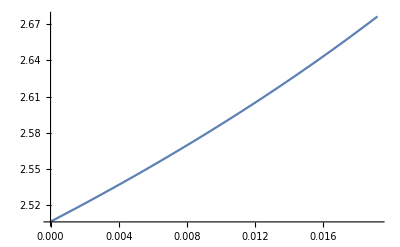

```mathematica
Plot[NIntegrate[f0 1/(√(π (s-t))), {t,0,s}], {s,0,cp}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.019192230336144673633516999594876523006660354263442880815635340017}. NIntegrate obtained 2.68893-4.81355×10^-7 ⅈ and 8.10678×10^-6 for the integral and error estimates.

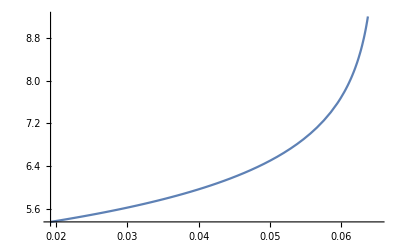

```mathematica
Plot[NIntegrate[f0 1/(√(π (s-t))), {t,0,cp}]+NIntegrate[f1 1/(√(π (s-t))),{t,cp,s}], {s,cp,cm}]
```

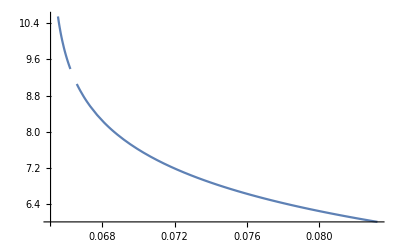

```mathematica
Plot[NIntegrate[f0 1/(√(π (s-t))), {t,0,cp}]+NIntegrate[f1 1/(√(π (s-t))),{t,cp,cm}]+NIntegrate[f2m 1/(√(π (s-t))), {t,cm,s}], {s,cm,cm+0.0181}]
```

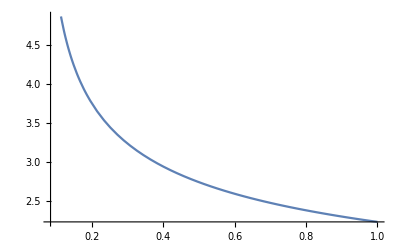

```mathematica
Plot[NIntegrate[f0 1/(√(π (s-t))), {t,0,cp}]+NIntegrate[f1 1/(√(π (s-t))),{t,cp,cm}]+NIntegrate[f2m 1/(√(π (s-t))), {t,cm,cm+0.0181}]+NIntegrate[f2 1/(√(π (s-t))), {t,cm+0.0181,s}], {s,cm+0.0181,1}]
```

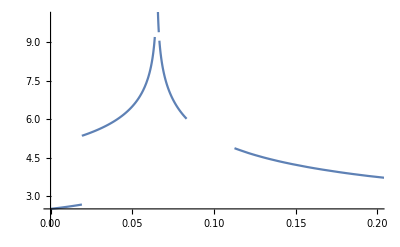

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,PlotRange->{{0,0.2},{2,10}}, GridLines->{{cm,cp},{}}]
```

```mathematica
Sum[1/((2ell-m)!)Binomial[2ell-m,m] a^m Gamma[3ell-m+1/2], {m,0,ell}]
```

(Gamma[1/2 (1+6 ell)] Hypergeometric2F1[1/2-ell,-ell,1/2-3 ell,-4 a])/Gamma[1+2 ell]

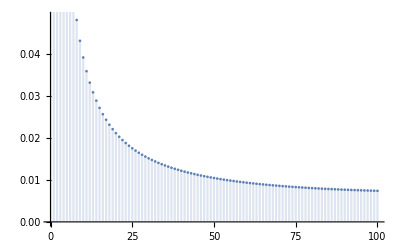

```mathematica
uval=0.029;
γ2=(1.05)^2;
DiscretePlot[√2((32γ2)/9 uval)^ell Gamma[1/2 (1+6 ell)]/Gamma[1+2 ell] Hypergeometric2F1[1/2-ell,-ell,1/2-3 ell,-9/(8γ2)]/(ell!), {ell,0,100}]
```

```mathematica
γ2=(1.05)^2;
√2((32γ2)/9)^ell Gamma[1/2 (1+6 ell)]/Gamma[1+2 ell] Hypergeometric2F1[1/2-ell,-ell,1/2-3 ell,-9/(8γ2)] /. ell->0
```

2.50663

```mathematica
γ2=(1.05)^2;
uval=0.029;
NSum[√2((32γ2)/9 uval)^ell Gamma[1/2 (1+6 ell)]/Gamma[1+2 ell] Hypergeometric2F1[1/2-ell,-ell,1/2-3 ell,-9/(8γ2)]/(ell!), {ell,0,∞}]
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

4.50167

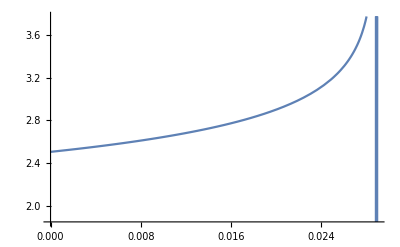

```mathematica
γ2=(1.05)^2;
Plot[2.5066282746310007+NSum[√2((32γ2)/9 u)^ell Gamma[1/2 (1+6 ell)]/Gamma[1+2 ell] Hypergeometric2F1[1/2-ell,-ell,1/2-3 ell,-9/(8γ2)]/(ell!), {ell,1,∞}],{u,0,0.029}]
```

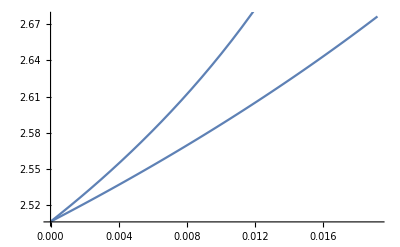

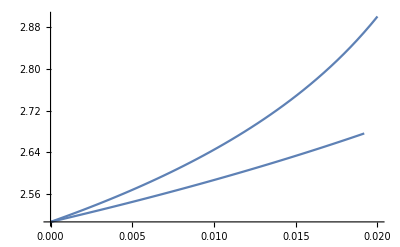

```mathematica
Show[-Graphics-,%]
```

```mathematica
D[Tanh[t/√2], {t,1}]
D[Tanh[t/√2], {t,2}]
```

Sech[t/(√2)]^2/(√2)

-Sech[t/(√2)]^2 Tanh[t/(√2)]

```mathematica
Integrate[1/(2 Cosh[t/√2]^4), {t,-∞,∞}]
N[%]
```

(2 √2)/3

0.942809

```mathematica
FullSimplify[x^2/2-2 x^3/3+x^4/4 /. x->(1/2)(Tanh[t/√2]+1)]
Integrate[FullSimplify[1/(4 Cosh[t/√2]^4)+%], {t,-∞,∞}]
N[%]
```

1/192 (1+Tanh[t/(√2)])^2 (11+Tanh[t/(√2)] (-10+3 Tanh[t/(√2)]))

Integrate::idiv: Integral of 9/32 Sech[t/(√2)]^4+1/48 ⅇ^(√2 t) Sech[t/(√2)]^4+1/192 ⅇ^(2 √2 t) Sech[t/(√2)]^4 does not converge on {-∞,∞}.

∫_(-∞)^∞ 1/192 (54+4 ⅇ^(√2 t)+ⅇ^(2 √2 t)) Sech[t/(√2)]^4ⅆt

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {253.438}. NIntegrate obtained 22.4144 and 0.270601 for the integral and error estimates.

22.4144